# Ibraheem Al-Yousef PHYS422 HW.1 28/1/2023

## Problem 1):

```mathematica
Subscript[ψ, 1]=A ⅇ^(ⅈ Subscript[k, 1] x)+b ⅇ^(-ⅈ Subscript[k, 1] x);
Subscript[ψ, 2]=d ⅇ^(-ⅈ Subscript[k, 2] x)+c ⅇ^(ⅈ Subscript[k, 2] x);
Subscript[ψ, 3]=f ⅇ^(ⅈ Subscript[k, 3] x);
fSol=f/.Solve[{Subscript[ψ, 1]==Subscript[ψ, 2]/.x->0,D[Subscript[ψ, 1],x]==D[Subscript[ψ, 2],x]/.x->0,Subscript[ψ, 3]==Subscript[ψ, 2]/.x->a,D[Subscript[ψ, 3],x]==D[Subscript[ψ, 2],x]/.x->a},{b,c,d,f}][[1]];
```

```mathematica
T=1/A^2 FullSimplify@((ComplexExpand@Abs[fSol]/.Subscript[k, 1]->Subscript[k, 3]/.Subscript[k, 2]->√(2m (Ε-Subscript[V, 0])/ℏ^2)/.Subscript[k, 3]->√(2m Ε/ℏ^2))^2)/.a->1/.ℏ->1/.m->1
```

(4 Ε (Ε-V_0))/(4 Ε^2-4 Ε V_0+Sin[√2 √(Ε-V_0)]^2 V_0^2)

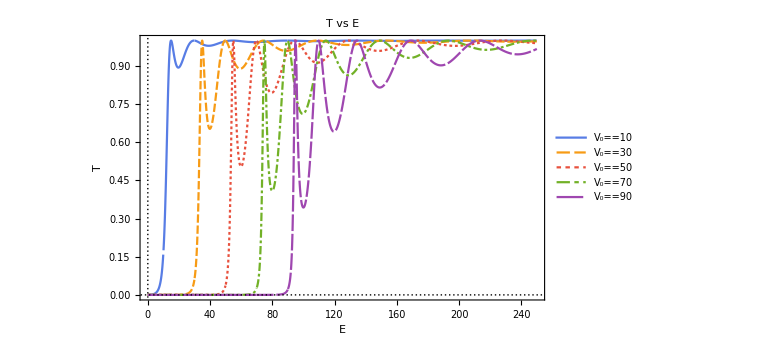

```mathematica
plt=Table[T,{Subscript[V, 0],10,100,20}];
Plot[plt,{Ε,0,250},PlotRange->All,PlotTheme->{"Scientific","BoldColor","Monochrome"},FrameLabel->{"Ε","T"},PlotLegends->Table[TraditionalForm[Subscript[V, 0]==t],{t,10,100,20}],ImageSize->Large,PlotLabel->"T vs Ε"]
```

We can notice that the Transmission coefficient is almost zero when E < V_0. Moreover, when E > V_0, the transmission is not always 1, it oscillates closer to 1 as E gets bigger.

## Problem 3):

We first solve Schrodinger’s equation for two regions, the first is when 0<x<a. The second is when x>a:

```mathematica
ψ1=(ψ[x]/.Assuming[m>0&&Ε>0&&Subscript[V, 0]>0,DSolve[{-ℏ^2/(2m)D[ψ[x],{x,2}]-Subscript[V, 0] ψ[x]==Ε ψ[x],ψ[0]==0},ψ[x],x]])[[1]]/.C[1]->A;
```

```mathematica
Assuming[m>0&&Ε>0&&Subscript[V, 0]>0&&a>0,FullSimplify[ψ1]/.(√(2(Ε+Subscript[V, 0]) m))/ℏ->α]//TraditionalForm
```

-2 ⅈ A sin(α x)

```mathematica
ψ2=(ψ[x]/.DSolve[-ℏ^2/(2m)D[ψ[x],{x,2}]==Ε ψ[x],ψ[x],x])[[1]];
```

```mathematica
Assuming[m>0&&Ε>0&&Subscript[V, 0]>0&&a>0,FullSimplify[ψ2]/.(√(2Ε m))/ℏ->k]//TraditionalForm
```

1 cos(k x)+2 sin(k x)

α=(√(2(Ε+V_0) m))/ℏ; k=(√(2Ε m))/ℏ. Now we apply the continuity of the wavefunction and its derivative at the boundary x=a. The solutions of the coefficients are in terms of A:

```mathematica
Sol=Solve[{ψ2==ψ1,D[ψ1,x]==D[ψ2,x]}/.x->a,{C[1],C[2]}];
Assuming[m>0&&Ε>0&&Subscript[V, 0]>0&&a>0,FullSimplify[Sol]/.(√(2(Ε+Subscript[V, 0]) m))/ℏ->α/.(√(2Ε m))/ℏ->k][[1]]//TraditionalForm
```

{1→-2 ⅈ A (sin(a α) cos(a k)-√((Ε+V_0)/Ε) cos(a α) sin(a k)),2→-2 ⅈ A (sin(a α) sin(a k)+√((Ε+V_0)/Ε) cos(a α) cos(a k))}

## Problem 7):

a)

b)

c)

d)


This is a "minimum-uncertainty" wave packet because it has the minimum Δx possible and the minimum Δp_x possible. This restriction is described in the uncertainty principle Δx Δp_x>=h/(4π).

## Problem 15):

a) “f” means =3. Therefore

b)

c)

d)